## Объявление глобальных переменных

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.01;horizSize=0.03;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

## Построение одного графика

### Импорт табличных данных

```mathematica
data=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/4sem/452/tables/v3.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
data//TableForm
```

β | h4 | h3 | h2 | h1 | V | δ | V1 | V3 |  | 
90. | 30. | 24. | 25. | 1. | 0.11 | 25. | 0.38 | 0.29 | 0.001 | 0.
80. | 30. | 24. | 25. | 2. | 0.11 | 12.5 | 0.52 | 0.21 | 0.174 | 0.03
75. | 31. | 25. | 24. | 3. | 0.11 | 8. | 0.63 | 0.17 | 0.259 | 0.07
65. | 36. | 26. | 24. | 6. | 0.16 | 4. | 0.8 | 0.2 | 0.423 | 0.18
55. | 42. | 27. | 24. | 10. | 0.22 | 2.4 | 0.91 | 0.24 | 0.574 | 0.33
45. | 47. | 26. | 24. | 12. | 0.29 | 2. | 0.94 | 0.31 | 0.707 | 0.5
35. | 58. | 28. | 24. | 19. | 0.35 | 1.3 | 0.99 | 0.35 | 0.819 | 0.67
25. | 59. | 34. | 24. | 18. | 0.27 | 1.3 | 0.99 | 0.4 | 0.906 | 0.82
15. | 64. | 33. | 24. | 20. | 0.32 | 1.2 | 1. | 0.46 | 0.966 | 0.93
5. | 66. | 20. | 24. | 20. | 0.53 | 1.2 | 1. | 0.54 | 0.996 | 0.99

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

0.15059+0.369731 Abs[Cos[1/180 π (17+x)]]

0.206689+0.374318 Cos[1/180 π (17+x)]^2

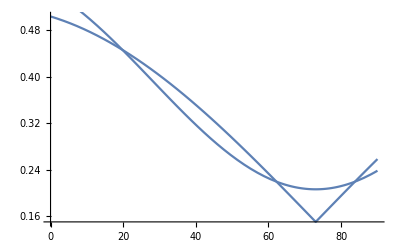

```mathematica
forFit=data⟦2;;,{1,9}⟧;
fit=Fit[forFit,{1,Abs[Cos[(x+17)*Pi/180]]},x]
fit2=Fit[forFit,{1,(Cos[(x+17)*Pi/180])^2},x]
Show[Plot[fit, {x, 0, 90}],
Plot[fit2, {x, 0, 90}]]
```

```mathematica
forFit1=data⟦2;;,{10,9}⟧;
forFit2=data⟦2;;,{11,9}⟧;
```

```mathematica
fitc = Fit[forFit1, {1,x},x]
fitc2 = Fit[forFit2, {1,x},x]
```

0.158591+0.271947 x

0.186757+0.288149 x

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные без крестов

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y}.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

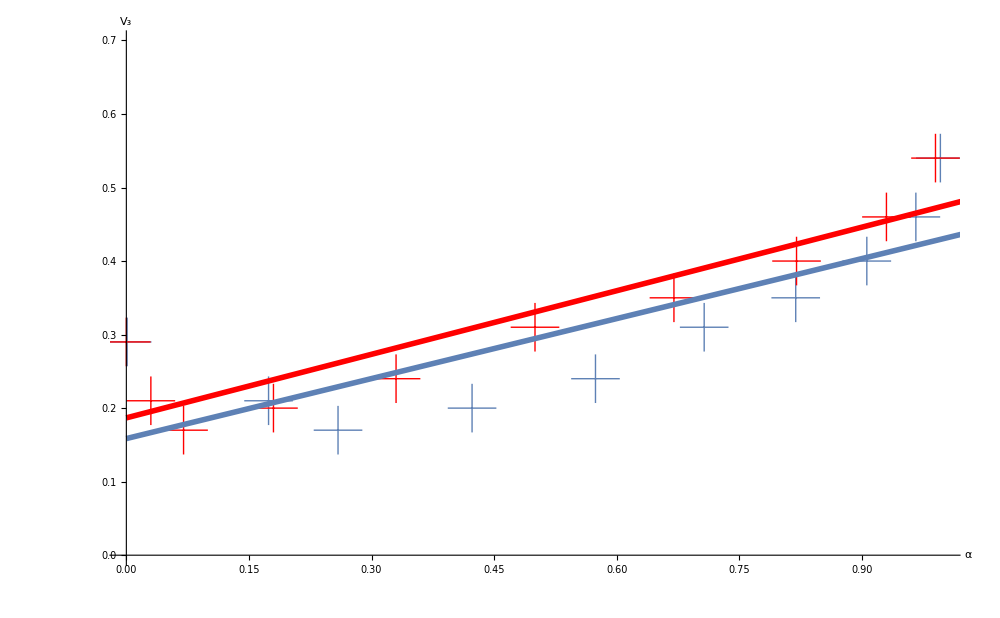

```mathematica
Show[ListPlot[data⟦2;;,{10,9}⟧,
GridLines->{grids@5,grids@0.1},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"α","V_3"},
AxesStyle->Directive[Large,Black],ImageSize->1000,
PlotStyle->{Thickness@0.1},
PlotMarkers->{"+", 50},
(*Joined->True,*)
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{0,1},{0,0.699}}],
ListPlot[data⟦2;;,{11,9}⟧,
GridLines->{grids@5,grids@0.1},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"α","V_3"},
AxesStyle->Directive[Large,Black],ImageSize->1000,
PlotStyle->{Thickness@0.1 ,Red},
PlotMarkers->{"+", 50},
(*Joined->True,*)
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{0,1},{0,0.699}}], 
Plot[fitc,{x,0,99}, PlotStyle->Thickness@0.004],
Plot[fitc2,{x,0,99}, PlotStyle->{Thickness@0.004, Red}]]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,4,5,5}⟧,
GridLines->{grids@0.5,grids@0.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"X","Y"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{0,6.9},{0,15}}], 
Plot[fit["Function"]@x,{x,0,35}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX=MapAt[dropLastDot@*ToString,data,{{2;;,All}}];
forTeX//TeXForm
```

\left(
\begin{array}{ccccccccc}
 \beta  & \text{h4} & \text{h3} & \text{h2} & \text{h1} & \text{V} & \delta  & \text{V1} & \text{V3} \\
 90 & 30 & 24 & 25 & 1 & 0.11 & 25 & 0.38 & 0.29 \\
 80 & 30 & 24 & 25 & 2 & 0.11 & 12.5 & 0.52 & 0.21 \\
 75 & 31 & 25 & 24 & 3 & 0.11 & 8 & 0.63 & 0.17 \\
 65 & 36 & 26 & 24 & 6 & 0.16 & 4 & 0.8 & 0.2 \\
 55 & 42 & 27 & 24 & 10 & 0.22 & 2.4 & 0.91 & 0.24 \\
 45 & 47 & 26 & 24 & 12 & 0.29 & 2 & 0.94 & 0.31 \\
 35 & 58 & 28 & 24 & 19 & 0.35 & 1.3 & 0.99 & 0.35 \\
 25 & 59 & 34 & 24 & 18 & 0.27 & 1.3 & 0.99 & 0.4 \\
 15 & 64 & 33 & 24 & 20 & 0.32 & 1.2 & 1 & 0.46 \\
 5 & 66 & 20 & 24 & 20 & 0.53 & 1.2 & 1 & 0.54 \\
\end{array}
\right)